```mathematica
ShowGraph5Least[alfa1Key]
```

-Graphics-361660

```mathematica
Map[ShowGraph5Least, Select[Keys[allGraphs5],allGraphs5[#,"vertexsets"]==allGraphs5[alfa1Key,"vertexsets"]&]]
```

{-Graphics-361380,-Graphics-361660,-Graphics-354060,-Graphics-354340,-Graphics-140161,-Graphics-140441,-Graphics-132842,-Graphics-133121}

```mathematica
ShowGraph5Least[beta1Key]
```

-Graphics-317380

```mathematica
Map[ShowGraph5Least, Select[Keys[allGraphs5],allGraphs5[#,"vertexsets"]==allGraphs5[beta1Key,"vertexsets"]&]]
```

{-Graphics-317380,-Graphics-314920,-Graphics-251680,-Graphics-249220,-Graphics-112441,-Graphics-109981,-Graphics-46741,-Graphics-44282}

```mathematica
Map[ShowGraph5Least, Select[Keys[allGraphs5],allGraphs5[#,"vertexsets"]==allGraphs5[gamma1Key,"vertexsets"]&]]
```

{-Graphics-296080,-Graphics-293281,-Graphics-223180,-Graphics-220381,-Graphics-77380,-Graphics-74581,-Graphics-4480,-Graphics-1682}

```mathematica
Map[ShowGraph5Least, Select[Keys[allGraphs5],allGraphs5[#,"vertexsets"]==allGraphs5[delta1Key,"vertexsets"]&]]
```

{-Graphics-361120,-Graphics-360300,-Graphics-339160,-Graphics-338340,-Graphics-154541,-Graphics-153721,-Graphics-132581,-Graphics-131762}

```mathematica
Map[ShowGraph5Least, Select[Keys[allGraphs5],allGraphs5[#,"vertexsets"]==allGraphs5[epsilon1Key,"vertexsets"]&]]
```

{-Graphics-317140,-Graphics-314440,-Graphics-244141,-Graphics-241441,-Graphics-119500,-Graphics-116800,-Graphics-46501,-Graphics-43802}

```mathematica
Map[ShowGraph5Least, Select[Keys[allGraphs5],allGraphs5[#,"vertexsets"]==allGraphs5[quad1Key,"vertexsets"]&&EdgeCount[allGraphs5[#,"graph"]]==0&]]
```

{-Graphics-1312210}

## Do the work

```mathematica
repEmpty=Table[k->First[Select[Keys[allGraphs5],allGraphs5[#,"vertexsets"]==allGraphs5[k,"vertexsets"]&&EdgeCount[allGraphs5[#,"graph"]]==0&]],{k,Join[alfa1s,{K5Key}]}]
```

{36166→13284,31738→4428,29608→168,36112→13176,31714→4380,29524→0}

```mathematica
repEmpty=Table[k->First[Select[Keys[allGraphs5],allGraphs5[#,"vertexsets"]==allGraphs5[k,"vertexsets"]&&EdgeCount[allGraphs5[#,"graph"]]==0&]],{k,quads}]
```

{36085→13122,29605→162,29527→6,31711→4374,29551→54}

```mathematica
repEmpty=Table[allGraphs5AtomKeys[[pos]]->Bases["T","AtomKeys"][[pos]],{pos,Flatten[Table[Position[allGraphs5AtomKeys,k],{k,alfa1s}]]}]
```

{36166→31224,31738→50718,29608→33130,36112→24414,31714→55252}

```mathematica
repEmpty=Table[k->First[Select[Bases["T","AtomKeys"],allGraphs5[#,"vertexsets"]==allGraphs5[k,"vertexsets"]&]],{k,Join[alfa1s,{K5Key}]}]
```

{36166→35434,31738→25168,29608→22318,36112→33916,31714→24414,29524→19936}

```mathematica
repEmpty=Table[k->First[Select[Bases["F","AtomKeys"],SymbolToSets[allGraphs5[#,"colofournull"]]==allGraphs5[k,"vertexsets"]&]],{k,alfa1s}]
```

{36166→6642,31738→2214,29608→84,36112→6588,31714→2190}

```mathematica
Map[ShowGraph5Least[#[[1]]]->ShowGraph5Least[#[[2]]]&,repEmpty]
```

{-Graphics-361660→-Graphics-664216,-Graphics-317380→-Graphics-221416,-Graphics-296080→-Graphics-8416,-Graphics-361120→-Graphics-658816,-Graphics-317140→-Graphics-219016}

```mathematica
(*newKeys=allGraphs5AtomKeys/.{alfa1Key->14044,beta1Key->11244, gamma1Key->29328,delta1Key->15454,epsilon1Key->24414}*)
```

```mathematica
newKeys=allGraphs5AtomKeys/.repEmpty
```

{29524,29525,29527,29533,29537,29551,29560,29605,84,29633,29767,29768,29797,29857,29888,30253,30262,30334,30496,30586,31711,2190,2214,31954,31984,32441,32684,36085,36086,6588,6642,36194,36817,36898,38281,38308,39014,49207,49208,49210,49216,49220,49963,49972,51475,51478,52232,56011,56012,56770,58288,59048}

```mathematica
Length[newKeys]
```

52

```mathematica
Table[ShowGraph5Least[k],{k,newKeys}]
```

{-Graphics-295240,-Graphics-295250,-Graphics-295270,-Graphics-295330,-Graphics-295371,-Graphics-295510,-Graphics-295600,-Graphics-296050,-Graphics-8416,-Graphics-296330,-Graphics-297670,-Graphics-297681,-Graphics-297970,-Graphics-298571,-Graphics-298881,-Graphics-302530,-Graphics-302621,-Graphics-303340,-Graphics-304961,-Graphics-305861,-Graphics-317110,-Graphics-219016,-Graphics-221416,-Graphics-319540,-Graphics-319840,-Graphics-324411,-Graphics-326841,-Graphics-360850,-Graphics-360860,-Graphics-658816,-Graphics-664216,-Graphics-361940,-Graphics-368170,-Graphics-368980,-Graphics-382810,-Graphics-383080,-Graphics-390141,-Graphics-492070,-Graphics-492081,-Graphics-492100,-Graphics-492161,-Graphics-492201,-Graphics-499631,-Graphics-499721,-Graphics-514750,-Graphics-514780,-Graphics-522321,-Graphics-560111,-Graphics-560121,-Graphics-567701,-Graphics-582881,-Graphics-590481}

```mathematica
Table[allGraphs5[k,"jake"]=PartitionToSymbol[allGraphs5[k,"vertexsets"],"w"],{k,newKeys}]
```

{w1x2x3x4x5,w1x2x3x45,w1x2x35x4,w1x2x34x5,w1x2x345,w1x25x3x4,w1x25x34,w1x24x3x5,w1x2x3x4x5,w1x245x3,w1x23x4x5,w1x23x45,w1x235x4,w1x234x5,w1x2345,w15x2x3x4,w15x2x34,w15x24x3,w15x23x4,w15x234,w14x2x3x5,w1x2x3x4x5,w1x2x3x4x5,w14x23x5,w14x235,w145x2x3,w145x23,w13x2x4x5,w13x2x45,w1x2x3x4x5,w1x2x3x4x5,w13x245,w135x2x4,w135x24,w134x2x5,w134x25,w1345x2,w12x3x4x5,w12x3x45,w12x35x4,w12x34x5,w12x345,w125x3x4,w125x34,w124x3x5,w124x35,w1245x3,w123x4x5,w123x45,w1235x4,w1234x5,w12345}

```mathematica
fullVariables=Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}]
```

{v1x2x3x4x5,v1x2x3x45,v1x2x35x4,v1x2x34x5,v1x2x345,v1x25x3x4,v1x25x34,v1x24x3x5,v1x24x35,v1x245x3,v1x23x4x5,v1x23x45,v1x235x4,v1x234x5,v1x2345,v15x2x3x4,v15x2x34,v15x24x3,v15x23x4,v15x234,v14x2x3x5,v14x2x35,v14x25x3,v14x23x5,v14x235,v145x2x3,v145x23,v13x2x4x5,v13x2x45,v13x25x4,v13x24x5,v13x245,v135x2x4,v135x24,v134x2x5,v134x25,v1345x2,v12x3x4x5,v12x3x45,v12x35x4,v12x34x5,v12x345,v125x3x4,v125x34,v124x3x5,v124x35,v1245x3,v123x4x5,v123x45,v1235x4,v1234x5,v12345}

```mathematica
Table[
allGraphs5[k,"jake"]==allGraphs5[k,"colofour"]
,
{k,newKeys}
]
```

{w1x2x3x4x5==v1x2x3x4x5,w1x2x3x45==v1x2x3x45,w1x2x35x4==v1x2x35x4,w1x2x34x5==v1x2x34x5,w1x2x345==v1x2x345,w1x25x3x4==v1x25x3x4,w1x25x34==v1x25x34,w1x24x3x5==v1x24x3x5,w1x2x3x4x5==v123x45+v123x4x5+v125x34+v125x3x4+v12x34x5+v12x3x45+v12x3x4x5+v134x25+v134x2x5+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x23x5+v14x25x3+v14x2x3x5+v15x23x4+v15x2x34+v15x2x3x4+v1x23x45+v1x23x4x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,w1x245x3==v1x245x3,w1x23x4x5==v1x23x4x5,w1x23x45==v1x23x45,w1x235x4==v1x235x4,w1x234x5==v1x234x5,w1x2345==v1x2345,w15x2x3x4==v15x2x3x4,w15x2x34==v15x2x34,w15x24x3==v15x24x3,w15x23x4==v15x23x4,w15x234==v15x234,w14x2x3x5==v14x2x3x5,w1x2x3x4x5==v123x45+v123x4x5+v125x34+v125x3x4+v12x34x5+v12x3x45+v12x3x4x5+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x45+v1x23x4x5+v1x245x3+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5,w1x2x3x4x5==v123x45+v123x4x5+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v135x24+v135x2x4+v13x24x5+v13x2x45+v13x2x4x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x45+v1x23x4x5+v1x24x35+v1x24x3x5+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w14x23x5==v14x23x5,w14x235==v14x235,w145x2x3==v145x2x3,w145x23==v145x23,w13x2x4x5==v13x2x4x5,w13x2x45==v13x2x45,w1x2x3x4x5==v124x35+v124x3x5+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v145x23+v145x2x3+v14x23x5+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x45+v1x23x4x5+v1x24x35+v1x24x3x5+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w1x2x3x4x5==v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x23x4+v15x2x34+v15x2x3x4+v1x235x4+v1x23x45+v1x23x4x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,w13x245==v13x245,w135x2x4==v135x2x4,w135x24==v135x24,w134x2x5==v134x2x5,w134x25==v134x25,w1345x2==v1345x2,w12x3x4x5==v12x3x4x5,w12x3x45==v12x3x45,w12x35x4==v12x35x4,w12x34x5==v12x34x5,w12x345==v12x345,w125x3x4==v125x3x4,w125x34==v125x34,w124x3x5==v124x3x5,w124x35==v124x35,w1245x3==v1245x3,w123x4x5==v123x4x5,w123x45==v123x45,w1235x4==v1235x4,w1234x5==v1234x5,w12345==v12345}

```mathematica
repFullToNew=ToRules[
Reduce[
Table[
allGraphs5[k,"jake"]==allGraphs5[k,"colofour"]
,
{k,newKeys}
],
fullVariables
]
];
```

```mathematica
repFullToNew
```

{v1x2x3x4x5→w1x2x3x4x5,v1x2x3x45→w1x2x3x45,v1x2x35x4→w1x2x35x4,v1x2x34x5→w1x2x34x5,v1x2x345→w1x2x345,v1x25x3x4→w1x25x3x4,v1x25x34→w1x25x34,v1x24x3x5→w1x24x3x5,v1x24x35→-w123x45/2-w123x4x5/2-w124x35/2-w124x3x5/2+w125x34/2+w125x3x4/2-w12x345/2-w12x34x5/2-w12x35x4/2-w12x3x45/2-w12x3x4x5/2-w134x25/2-w134x2x5/2-w135x24/2-w135x2x4/2+w13x245/2-w13x2x45/2-w13x2x4x5/2-w145x23/2-w145x2x3/2+w14x235/2-w14x23x5/2-w14x2x3x5/2-w15x234/2-w15x23x4/2-w15x24x3/2-w15x2x34/2-w15x2x3x4/2-w1x234x5/2+w1x235x4/2-w1x23x45/2-w1x23x4x5/2+w1x245x3/2-w1x24x3x5/2+w1x25x34/2+w1x25x3x4/2-w1x2x345/2-w1x2x34x5/2-w1x2x35x4/2-w1x2x3x45/2,v1x245x3→w1x245x3,v1x23x4x5→w1x23x4x5,v1x23x45→w1x23x45,v1x235x4→w1x235x4,v1x234x5→w1x234x5,v1x2345→w1x2345,v15x2x3x4→w15x2x3x4,v15x2x34→w15x2x34,v15x24x3→w15x24x3,v15x23x4→w15x23x4,v15x234→w15x234,v14x2x3x5→w14x2x3x5,v14x2x35→w123x45/2+w123x4x5/2-w124x35/2-w124x3x5/2-w125x34/2-w125x3x4/2-w12x345/2-w12x34x5/2-w12x35x4/2-w12x3x45/2-w12x3x4x5/2+w134x25/2+w134x2x5/2+w135x24/2+w135x2x4/2-w13x245/2+w13x2x45/2+w13x2x4x5/2-w145x23/2-w145x2x3/2-w14x235/2-w14x23x5/2-w14x2x3x5/2-w15x234/2-w15x23x4/2-w15x24x3/2-w15x2x34/2-w15x2x3x4/2-w1x234x5/2-w1x235x4/2-w1x23x45/2-w1x23x4x5/2-w1x245x3/2-w1x24x3x5/2-w1x25x34/2-w1x25x3x4/2-w1x2x345/2-w1x2x34x5/2-w1x2x35x4/2-w1x2x3x45/2,v14x25x3→-w123x45/2-w123x4x5/2+w124x35/2+w124x3x5/2-w125x34/2-w125x3x4/2-w12x345/2-w12x34x5/2-w12x35x4/2-w12x3x45/2-w12x3x4x5/2-w134x25/2-w134x2x5/2-w135x24/2-w135x2x4/2+w13x245/2-w13x2x45/2-w13x2x4x5/2-w145x23/2-w145x2x3/2-w14x235/2-w14x23x5/2-w14x2x3x5/2+w15x234/2-w15x23x4/2+w15x24x3/2-w15x2x34/2-w15x2x3x4/2+w1x234x5/2-w1x235x4/2-w1x23x45/2-w1x23x4x5/2+w1x245x3/2+w1x24x3x5/2-w1x25x34/2-w1x25x3x4/2-w1x2x345/2-w1x2x34x5/2-w1x2x35x4/2-w1x2x3x45/2,v14x23x5→w14x23x5,v14x235→w14x235,v145x2x3→w145x2x3,v145x23→w145x23,v13x2x4x5→w13x2x4x5,v13x2x45→w13x2x45,v13x25x4→-w123x45/2-w123x4x5/2-w124x35/2-w124x3x5/2-w125x34/2-w125x3x4/2+w12x345/2-w12x34x5/2+w12x35x4/2-w12x3x45/2-w12x3x4x5/2-w134x25/2-w134x2x5/2+w135x24/2+w135x2x4/2-w13x245/2-w13x2x45/2-w13x2x4x5/2-w145x23/2-w145x2x3/2+w14x235/2-w14x23x5/2-w14x2x3x5/2-w15x234/2-w15x23x4/2-w15x24x3/2-w15x2x34/2-w15x2x3x4/2-w1x234x5/2+w1x235x4/2-w1x23x45/2-w1x23x4x5/2-w1x245x3/2-w1x24x3x5/2-w1x25x34/2-w1x25x3x4/2+w1x2x345/2-w1x2x34x5/2+w1x2x35x4/2-w1x2x3x45/2,v13x24x5→-w123x45/2-w123x4x5/2+w124x35/2+w124x3x5/2-w125x34/2-w125x3x4/2-w12x345/2-w12x34x5/2-w12x35x4/2-w12x3x45/2-w12x3x4x5/2+w134x25/2+w134x2x5/2-w135x24/2-w135x2x4/2-w13x245/2-w13x2x45/2-w13x2x4x5/2+w145x23/2+w145x2x3/2-w14x235/2+w14x23x5/2+w14x2x3x5/2-w15x234/2-w15x23x4/2-w15x24x3/2-w15x2x34/2-w15x2x3x4/2-w1x234x5/2-w1x235x4/2-w1x23x45/2-w1x23x4x5/2-w1x245x3/2-w1x24x3x5/2-w1x25x34/2-w1x25x3x4/2-w1x2x345/2-w1x2x34x5/2-w1x2x35x4/2-w1x2x3x45/2,v13x245→w13x245,v135x2x4→w135x2x4,v135x24→w135x24,v134x2x5→w134x2x5,v134x25→w134x25,v1345x2→w1345x2,v12x3x4x5→w12x3x4x5,v12x3x45→w12x3x45,v12x35x4→w12x35x4,v12x34x5→w12x34x5,v12x345→w12x345,v125x3x4→w125x3x4,v125x34→w125x34,v124x3x5→w124x3x5,v124x35→w124x35,v1245x3→w1245x3,v123x4x5→w123x4x5,v123x45→w123x45,v1235x4→w1235x4,v1234x5→w1234x5,v12345→w12345}

```mathematica
Monitor[
Table[
allGraphs5[k,"jake"]=Simplify[allGraphs5[k,"colofour"]/.repFullToNew],
{k,Sort[Keys[allGraphs5]]}
],k];
```

```mathematica
allGraphs5[0,"jake"]
```

1/2 (2 w12345+2 w1234x5+2 w1235x4-w123x45-w123x4x5+2 w1245x3+w124x35+w124x3x5-w125x34-w125x3x4-w12x345-3 w12x34x5-w12x35x4-3 w12x3x45-3 w12x3x4x5+2 w1345x2+w134x25+w134x2x5+w135x24+w135x2x4+w13x245-w13x2x45-w13x2x4x5-w145x23-w145x2x3+w14x235-w14x23x5-w14x2x3x5-w15x234-3 w15x23x4-w15x24x3-3 w15x2x34-3 w15x2x3x4+2 w1x2345-w1x234x5+w1x235x4-3 w1x23x45-3 w1x23x4x5+w1x245x3-w1x24x3x5-w1x25x34-w1x25x3x4-w1x2x345-3 w1x2x34x5-w1x2x35x4-3 w1x2x3x45+2 w1x2x3x4x5)

```mathematica
Bases["W"]=Association[];
```

```mathematica
Bases["W","Colofour"]="jake";
```

```mathematica
Bases["W"]
```

<|Colofour→jake|>

## Working with bases

```mathematica
MyComp:=CompareSymbols;
```

```mathematica
Table[Bases[base,"AtomKeys"]=Sort[Select[Keys[allGraphs5],Length[ListofVars[allGraphs5[#,Bases[base,"Colofour"]]]]==1&],MyComp[allGraphs5[#1,Bases[base,"Colofour"]],allGraphs5[#2,Bases[base,"Colofour"]]]&]
,{base,allBases}];
```

```mathematica
Table[Bases[base,"Variables"]=Table[allGraphs5[k,Bases[base,"Colofour"]],{k,Bases[base,"AtomKeys"]}]
,{base,allBases}];
```

```mathematica
BaseCoeff[key_,base_]:=Table[Coefficient[allGraphs5[key,Bases[base,"Colofour"]],var],{var,Bases[base,"Variables"]}]
```

```mathematica
BaseCoeff[0,"W"]
```

{1,1,1,1,1,1,-3/2,-3/2,-1/2,-3/2,-1/2,-1/2,-3/2,-1/2,-1/2,-3/2,-1/2,-3/2,-1/2,1/2,1/2,-1/2,-3/2,-3/2,-1/2,-1/2,1/2,-1/2,-1/2,1/2,1/2,-1/2,-1/2,-3/2,-3/2,-1/2,1,-1/2,-1/2,1,1,1/2,1,-1/2,1/2,1/2,1,1/2,1/2,-1/2,-1/2,1}

```mathematica
ConversionMatrix[base1_,base2_]:=Table[BaseCoeff[key1,base2],{key1,Bases[base1,"AtomKeys"]}]
```

```mathematica
Table[Bases[base,"AtomKeys"],{base,allBases}]//Flatten//DeleteDuplicates//Length
```

239

```mathematica
Clear[RepGraph];RepGraph[base_]:=RepGraph[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->ShowGraph5Least[key],{key,Bases[base,"AtomKeys"]}]
```

```mathematica
Clear[RepAtLeast];RepAtLeast[base_]:=RepAtLeast[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->allGraphs5[key,"atleast"],{key,Bases[base,"AtomKeys"]}]
```

```mathematica
Clear[RepChromial];RepChromial[base_]:=RepChromial[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->ChromaticPolynomial[allGraphs5[key,"graph"],x],{key,Bases[base,"AtomKeys"]}]
```

```mathematica
Clear[RepEmbed];RepEmbed[base_]:=RepEmbed[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->allGraphs5[key,"embed"],{key,Bases[base,"AtomKeys"]}]
```

```mathematica
RepEmbed["W"]
```

{w1x2x3x4x5→385,w1x2x3x4x5→368,w1x2x3x4x5→314,w1x2x3x4x5→314,w1x2x3x4x5→368,w1x2x3x4x5→0,w1x2x3x45→10,w1x2x34x5→20,w1x2x35x4→6,w1x23x4x5→10,w1x24x3x5→6,w1x25x3x4→11,w12x3x4x5→11,w13x2x4x5→9,w14x2x3x5→9,w15x2x3x4→11,w1x2x345→14,w1x23x45→14,w1x234x5→14,w1x235x4→10,w1x245x3→10,w1x25x34→31,w12x3x45→16,w12x34x5→29,w12x35x4→8,w123x4x5→20,w124x3x5→13,w125x3x4→21,w13x2x45→8,w134x2x5→7,w135x2x4→13,w14x23x5→8,w145x2x3→20,w15x2x34→29,w15x23x4→16,w15x24x3→8,w1x2345→11,w12x345→11,w123x45→12,w1234x5→16,w1235x4→18,w124x35→5,w1245x3→18,w125x34→26,w13x245→4,w134x25→9,w1345x2→16,w135x24→5,w14x235→4,w145x23→12,w15x234→11,w12345→16}

## pictures of

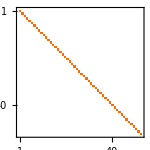
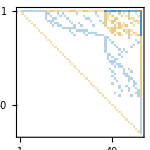
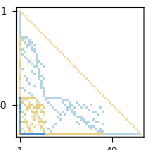
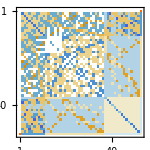
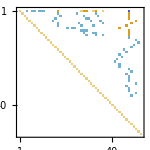
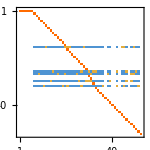
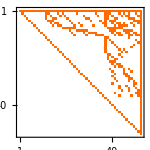
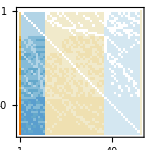
| C | E | G | F | T | W
C | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
E | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
G | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
F | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
T | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
W | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
TableForm[Table[MatrixPlot[ConversionMatrix[base1,base2],ImageSize->150],{base1,allBases},{base2,allBases}],TableHeadings->{allBases, allBases},TableAlignments->{Center, Center}]
```

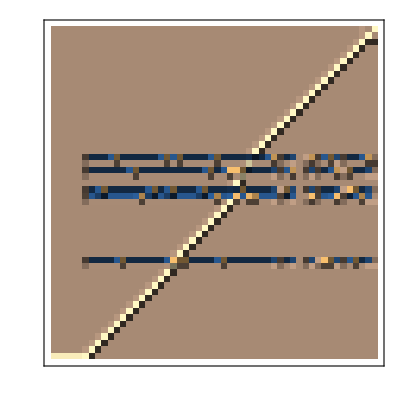

```mathematica
ConversionMatrix["C","W"]//ReliefPlot
```

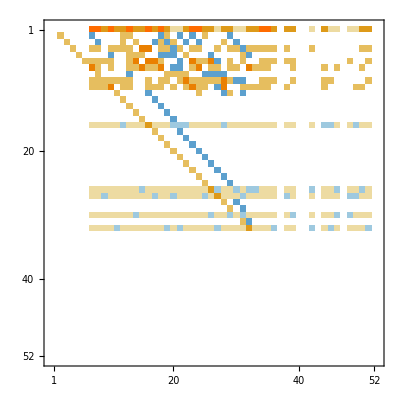

```mathematica
(ConversionMatrix["E","C"]-ConversionMatrix["E","W"])//MatrixPlot
```

```mathematica
repJake=Table[allGraphs5[k,"jake"]->ShowGraph5Least[k],{k,newKeys}];
```

```mathematica
allGraphs5[lambdaKey,"jake"]/.repJake
```

1/2 (-3 -Graphics-560121-3 -Graphics-499721-3 -Graphics-492201--Graphics-514780-3 -Graphics-326841-3 -Graphics-305861--Graphics-319840--Graphics-368980--Graphics-361940--Graphics-383080-3 -Graphics-560111--Graphics-514750-5 -Graphics-492161-3 -Graphics-499631-3 -Graphics-492100-5 -Graphics-492081--Graphics-382810-3 -Graphics-319540-3 -Graphics-298571--Graphics-368170-5 -Graphics-304961--Graphics-297970-3 -Graphics-360860-5 -Graphics-297681-3 -Graphics-324411-3 -Graphics-303340--Graphics-296330-5 -Graphics-302621-3 -Graphics-295600-3 -Graphics-295371-5 -Graphics-492070--Graphics-360850-5 -Graphics-297670--Graphics-317110--Graphics-296050-5 -Graphics-295330-5 -Graphics-302530--Graphics-295510-5 -Graphics-295250--Graphics-295270+2 -Graphics-295240)

```mathematica
allGraphs5[0,"jake"]/.repJake
```

1/2 (2 -Graphics-590481+2 -Graphics-582881+2 -Graphics-567701--Graphics-560121+2 -Graphics-522321--Graphics-499721--Graphics-492201+-Graphics-514780+2 -Graphics-390141--Graphics-326841--Graphics-305861+2 -Graphics-298881+-Graphics-319840+-Graphics-368980+-Graphics-361940+-Graphics-383080--Graphics-560111+-Graphics-514750-3 -Graphics-492161--Graphics-499631--Graphics-492100-3 -Graphics-492081+-Graphics-382810--Graphics-319540--Graphics-298571+-Graphics-368170-3 -Graphics-304961+-Graphics-297970--Graphics-360860-3 -Graphics-297681--Graphics-324411--Graphics-303340+-Graphics-296330-3 -Graphics-302621--Graphics-295600--Graphics-295371-3 -Graphics-492070--Graphics-360850-3 -Graphics-297670--Graphics-317110--Graphics-296050-3 -Graphics-295330-3 -Graphics-302530--Graphics-295510-3 -Graphics-295250--Graphics-295270+2 -Graphics-295240)

```mathematica
allGraphs5[lambdaKey,"atleast"]
```

3

```mathematica
allGraphs5[lambdaKey,"colotree"]
```

-t1345x2+t145x2x3-t15x2x3x4+t1x2x3x4x5

```mathematica
Table[ShowGraph5Least[k]->Simplify[(allGraphs5[k,"jake"]/.repJake)==0],{k,alfa1s}]//TableForm
```

-Graphics-361660→-Graphics-560121+-Graphics-499721+-Graphics-492201+-Graphics-305861+-Graphics-319840+-Graphics-368980+-Graphics-361940+-Graphics-560111+-Graphics-492161+-Graphics-499631+-Graphics-492100+-Graphics-492081+-Graphics-298571+-Graphics-368170+-Graphics-304961+-Graphics-297970+-Graphics-360860+-Graphics-297681+-Graphics-303340+-Graphics-296330+-Graphics-302621+-Graphics-295600+-Graphics-295371+-Graphics-492070+-Graphics-360850+-Graphics-297670+-Graphics-296050+-Graphics-295330+-Graphics-302530+-Graphics-295510+-Graphics-295250+-Graphics-295270==-Graphics-514780+-Graphics-326841+-Graphics-383080+-Graphics-514750+-Graphics-382810+-Graphics-319540+-Graphics-324411+-Graphics-317110
-Graphics-317380→-Graphics-560121+-Graphics-499721+-Graphics-492201+-Graphics-326841+-Graphics-319840+-Graphics-368980+-Graphics-383080+-Graphics-560111+-Graphics-492161+-Graphics-499631+-Graphics-492100+-Graphics-492081+-Graphics-382810+-Graphics-319540+-Graphics-368170+-Graphics-304961+-Graphics-297970+-Graphics-360860+-Graphics-297681+-Graphics-324411+-Graphics-302621+-Graphics-295600+-Graphics-295371+-Graphics-492070+-Graphics-360850+-Graphics-297670+-Graphics-317110+-Graphics-295330+-Graphics-302530+-Graphics-295510+-Graphics-295250+-Graphics-295270==-Graphics-514780+-Graphics-305861+-Graphics-361940+-Graphics-514750+-Graphics-298571+-Graphics-303340+-Graphics-296330+-Graphics-296050
-Graphics-296080→-Graphics-560121+-Graphics-492201+-Graphics-514780+-Graphics-326841+-Graphics-305861+-Graphics-368980+-Graphics-383080+-Graphics-560111+-Graphics-514750+-Graphics-492161+-Graphics-492100+-Graphics-492081+-Graphics-382810+-Graphics-319540+-Graphics-298571+-Graphics-368170+-Graphics-304961+-Graphics-360860+-Graphics-297681+-Graphics-324411+-Graphics-303340+-Graphics-302621+-Graphics-295371+-Graphics-492070+-Graphics-360850+-Graphics-297670+-Graphics-317110+-Graphics-296050+-Graphics-295330+-Graphics-302530+-Graphics-295250+-Graphics-295270==-Graphics-499721+-Graphics-319840+-Graphics-361940+-Graphics-499631+-Graphics-297970+-Graphics-296330+-Graphics-295600+-Graphics-295510
-Graphics-361120→-Graphics-560121+-Graphics-499721+-Graphics-514780+-Graphics-326841+-Graphics-305861+-Graphics-361940+-Graphics-383080+-Graphics-560111+-Graphics-514750+-Graphics-492161+-Graphics-499631+-Graphics-492081+-Graphics-382810+-Graphics-319540+-Graphics-298571+-Graphics-304961+-Graphics-360860+-Graphics-297681+-Graphics-324411+-Graphics-303340+-Graphics-296330+-Graphics-302621+-Graphics-295600+-Graphics-492070+-Graphics-360850+-Graphics-297670+-Graphics-317110+-Graphics-296050+-Graphics-295330+-Graphics-302530+-Graphics-295510+-Graphics-295250==-Graphics-492201+-Graphics-319840+-Graphics-368980+-Graphics-492100+-Graphics-368170+-Graphics-297970+-Graphics-295371+-Graphics-295270
-Graphics-317140→-Graphics-560121+-Graphics-368980+-Graphics-383080+-Graphics-560111+-Graphics-382810+-Graphics-368170+-Graphics-360860+-Graphics-360850==-Graphics-499721+-Graphics-492201+-Graphics-514780+-Graphics-326841+-Graphics-305861+-Graphics-319840+-Graphics-361940+-Graphics-514750+-Graphics-492161+-Graphics-499631+-Graphics-492100+-Graphics-492081+-Graphics-319540+-Graphics-298571+-Graphics-304961+-Graphics-297970+-Graphics-297681+-Graphics-324411+-Graphics-303340+-Graphics-296330+-Graphics-302621+-Graphics-295600+-Graphics-295371+-Graphics-492070+-Graphics-297670+-Graphics-317110+-Graphics-296050+-Graphics-295330+-Graphics-302530+-Graphics-295510+-Graphics-295250+-Graphics-295270

```mathematica
Keys[allGraphs5[0]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,parents,children,comp,compwhy,colofour,colortable,colofournull,colofourrealnull,atleast,atleastwhy,embed,colofourgenerator,colofourtree,colotree,jake}

```mathematica
allGraphs5[0,"embed"]
```

628

```mathematica
Map[FactorTerms,Simplify[(Total[Table[allGraphs5[k,"jake"],{k,alfa1s}]])==0]/.repJake]
```

3 -Graphics-560121+3 -Graphics-499721+3 -Graphics-492201+-Graphics-514780+3 -Graphics-326841+3 -Graphics-305861+-Graphics-319840+-Graphics-368980+-Graphics-361940+-Graphics-383080+3 -Graphics-560111+-Graphics-514750+5 -Graphics-492161+3 -Graphics-499631+3 -Graphics-492100+5 -Graphics-492081+-Graphics-382810+3 -Graphics-319540+3 -Graphics-298571+-Graphics-368170+5 -Graphics-304961+-Graphics-297970+3 -Graphics-360860+5 -Graphics-297681+3 -Graphics-324411+3 -Graphics-303340+-Graphics-296330+5 -Graphics-302621+3 -Graphics-295600+3 -Graphics-295371+5 -Graphics-492070+3 -Graphics-360850+5 -Graphics-297670+3 -Graphics-317110+3 -Graphics-296050+5 -Graphics-295330+5 -Graphics-302530+3 -Graphics-295510+5 -Graphics-295250+3 -Graphics-295270==0

```mathematica
Simplify[(Simplify[2*Total[Table[allGraphs5[k,"jake"],{k,alfa1s}]]]/.RepGraph["W"])==0]
```

3 -Graphics-560121+3 -Graphics-499721+3 -Graphics-492201+-Graphics-514780+3 -Graphics-326841+3 -Graphics-305861+-Graphics-319840+-Graphics-368980+-Graphics-361940+-Graphics-383080+3 -Graphics-560111+-Graphics-514750+5 -Graphics-492161+3 -Graphics-499631+3 -Graphics-492100+5 -Graphics-492081+-Graphics-382810+3 -Graphics-319540+3 -Graphics-298571+-Graphics-368170+5 -Graphics-304961+-Graphics-297970+3 -Graphics-360860+5 -Graphics-297681+3 -Graphics-324411+3 -Graphics-303340+-Graphics-296330+5 -Graphics-302621+3 -Graphics-295600+3 -Graphics-295371+5 -Graphics-492070+3 -Graphics-360850+5 -Graphics-297670+3 -Graphics-317110+3 -Graphics-296050+5 -Graphics-295330+5 -Graphics-302530+3 -Graphics-295510+5 -Graphics-295250+3 -Graphics-295270==0

```mathematica
Simplify[(Simplify[2*Total[Table[allGraphs5[k,"jake"],{k,quads}]]]/.RepGraph["W"])==0]
```

```mathematica
Simplify[(Simplify[2*Total[Table[allGraphs5[k,"jake"],{k,quads}]]]/.RepGraph["W"])==0]
```

-Graphics-360850+-Graphics-317110+-Graphics-296050+-Graphics-295510+-Graphics-295270==0

```mathematica
Map[FactorTerms,Simplify[(Total[Table[allGraphs5[k,"jake"],{k,quads}]]/.repJake)==0]]
```

-Graphics-360850+-Graphics-317110+-Graphics-296050+-Graphics-295510+-Graphics-295270==0

## Verifying the miracle

```mathematica
Fold[And,Table[allGraphs5[k,"embed"]==(allGraphs5[k,"jake"]/.RepEmbed["W"]),{k,Keys[allGraphs5]}]]
```

False

```mathematica
Table[{allGraphs5[k,"embed"],(allGraphs5[k,"jake"]/.RepEmbed["W"])},{k,Take[Keys[allGraphs5],10]}]
```

{{628,277/2},{388,-203/2},{306,369/2},{242,977/2},{167,827/2},{108,709/2},{92,477},{50,435},{16,401},{10,395}}

```mathematica
Select[Keys[allGraphs5],allGraphs5[#,"embed"]!=(allGraphs5[#,"colofour"]/.RepEmbed["C"])&]
```

{}